Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{1.53188,8.19662}

{8.28384,1.76083}

{2.58968,9.06392}

{0.121791,4.01876}

{9.33099,5.76037}

{0.987935,2.30193}

{9.24387,6.84731}

{3.77473,9.69839}

{8.33373,8.31122}

{7.36337,0.65172}

{8.38845,1.92293}

{6.30606,9.79132}

{6.73381,0.486984}

{5.41432,9.90503}

{9.02697,7.53826}

{0.451059,6.98961}

{5.65747,0.443866}

{9.33446,6.29975}

{0.134743,4.30403}

{2.67693,1.05082}

{8.58943,2.41724}

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{24.7862,21.4289}

{19.3961,15.2151}

{23.6399,17.0557}

{24.2058,18.011}

{16.3631,22.7815}

{21.9723,24.5312}

{24.6174,18.877}

{24.2367,22.4839}

{20.9225,15.1017}

{15.3585,18.2458}

{16.4254,17.0222}

{24.9499,20.4819}

{15.6094,22.0595}

{23.4135,23.6212}

{20.9737,24.8696}

{18.212,24.3232}

{18.2411,15.4533}

{22.9986,16.4976}

{18.7096,24.6052}

{{8.58943,2.41724},{2.67693,1.05082},{0.134743,4.30403},{9.33446,6.29975},{5.65747,0.443866},{0.451059,6.98961},{9.02697,7.53826},{5.41432,9.90503},{6.73381,0.486984},{6.30606,9.79132},{8.38845,1.92293},{7.36337,0.65172},{8.33373,8.31122},{3.77473,9.69839},{9.24387,6.84731},{0.987935,2.30193},{9.33099,5.76037},{0.121791,4.01876},{2.58968,9.06392},{8.28384,1.76083},{1.53188,8.19662}}

{{18.7096,24.6052},{22.9986,16.4976},{18.2411,15.4533},{18.212,24.3232},{20.9737,24.8696},{23.4135,23.6212},{15.6094,22.0595},{24.9499,20.4819},{16.4254,17.0222},{15.3585,18.2458},{20.9225,15.1017},{24.2367,22.4839},{24.6174,18.877},{21.9723,24.5312},{16.3631,22.7815},{24.2058,18.011},{23.6399,17.0557},{19.3961,15.2151},{24.7862,21.4289}}

{{8.33373,8.31122}}

{{18.2411,15.4533}}

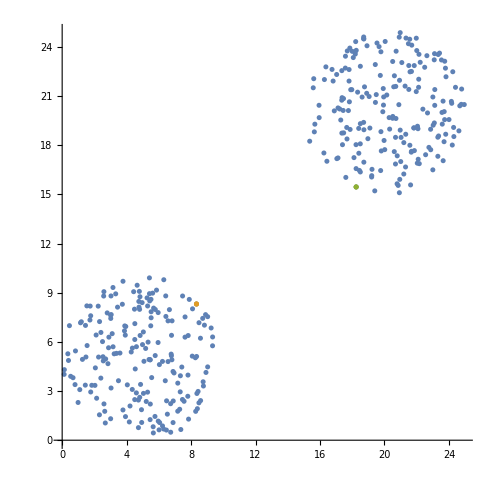

{{9.02697,7.53826}}

{{15.3585,18.2458}}

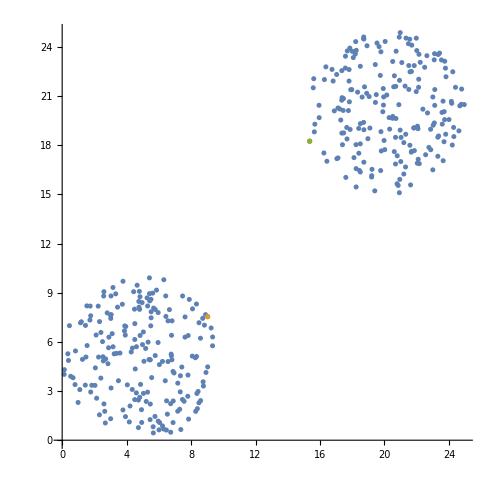

BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE

```mathematica
(*Global Variables*)
numOfPoints = 200;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*Initialize of two regions*)
region1 = DiscretizeRegion@Disk[{5,5},5];
region2 = DiscretizeRegion@Disk[{20, 20}, 5];
pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];

area = Join[pts1, pts2];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],Print[arrayOneConvexHull[[x]]], arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];

arrayTwoConvexHull = pts2;
cutConvexHull2[x_]=If[RegionMember[convexHullpts2,arrayTwoConvexHull[[x]]],Print[arrayTwoConvexHull[[x]]], arrayTwoConvexHull = Delete[arrayTwoConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull2[i]];

arrayOneConvexHull
arrayTwoConvexHull

(*Calculate nearest on ConvexHull*)
oneToTwoConvexHull = First[Nearest[arrayOneConvexHull,arrayTwoConvexHull]]
twoToOneConvexHull = First[Nearest[arrayTwoConvexHull,arrayOneConvexHull]]
ListPlot[{area, oneToTwoConvexHull, twoToOneConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
oneToTwo = First[Nearest[pts1,pts2]]
twoTo0ne= First[Nearest[pts2,pts1]]
ListPlot[{area, oneToTwo, twoTo0ne}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[(oneToTwo == oneToTwoConvexHull) && (twoTo0ne == twoToOneConvexHull),Print["BODY JSOU STEJNE"],
If[(ContainsAny[arrayOneConvexHull, oneToTwo])&&(ContainsAny[arrayTwoConvexHull, twoTo0ne]),Print["BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE"]], Print["JEDEN NEBO OBA BODY NEJSOU NA KONVEXNÍ OBÁLCE"] ]
```